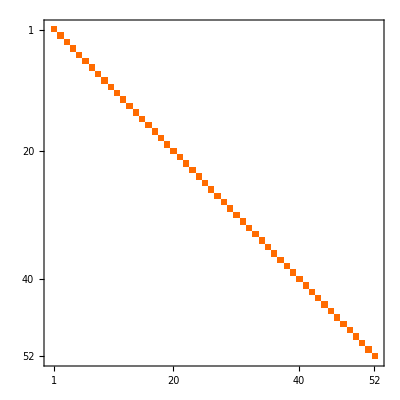
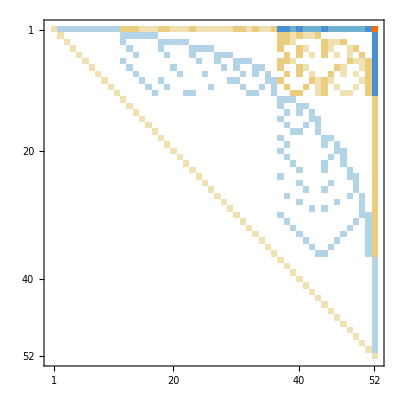
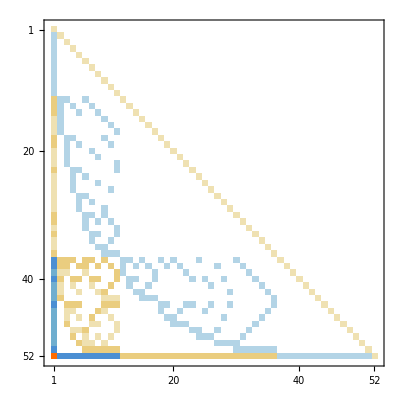
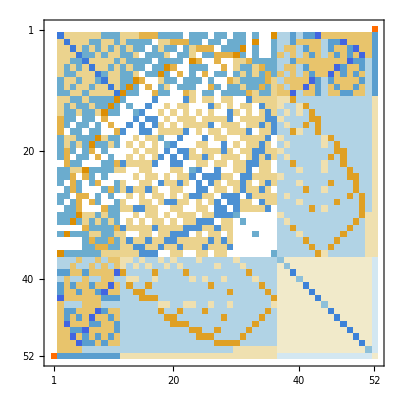
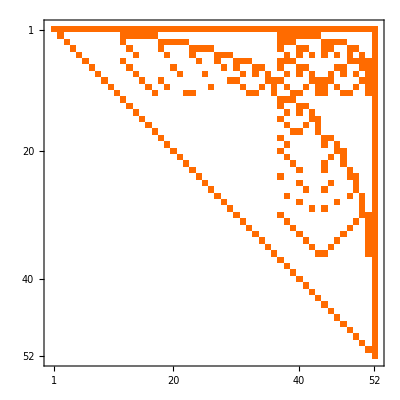
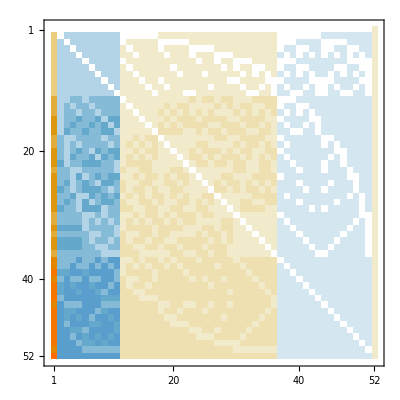
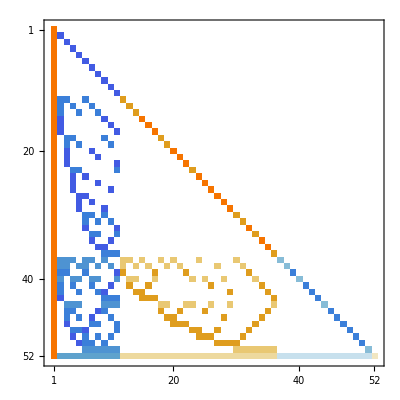
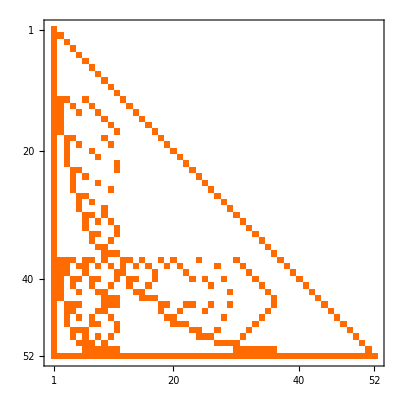
| C | E | G | F
C | -Graphics-C→C | -Graphics-C→E | -Graphics-C→G | -Graphics-C→F
E | -Graphics-E→C | -Graphics-E→E | -Graphics-E→G | -Graphics-E→F
G | -Graphics-G→C | -Graphics-G→E | -Graphics-G→G | -Graphics-G→F
F | -Graphics-F→C | -Graphics-F→E | -Graphics-F→G | -Graphics-F→F

```mathematica
With[{bases={"C","E","G","F"}},
TableForm[Table[Labeled[ConversionMatrix[base1,base2]//MatrixPlot,base1->base2],{base1,bases},{base2,bases}],TableHeadings->{bases, bases}]
]
```

```mathematica
ConversionMatrix["C","E"]==Transpose[ConversionMatrix["C","G"]]
```

True

```mathematica
(ConversionMatrix["C","G"].ConversionMatrix["F","E"]//Diagonal)*(Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols])
```

{v1x2x3x4x5,-v12x3x4x5,-v13x2x4x5,-v14x2x3x5,-v15x2x3x4,-v1x23x4x5,-v1x24x3x5,-v1x25x3x4,-v1x2x34x5,-v1x2x35x4,-v1x2x3x45,2 v123x4x5,2 v124x3x5,2 v125x3x4,v12x34x5,v12x35x4,v12x3x45,2 v134x2x5,2 v135x2x4,v13x24x5,v13x25x4,v13x2x45,2 v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,2 v1x234x5,2 v1x235x4,v1x23x45,2 v1x245x3,v1x24x35,v1x25x34,2 v1x2x345,-6 v1234x5,-6 v1235x4,-2 v123x45,-6 v1245x3,-2 v124x35,-2 v125x34,-2 v12x345,-6 v1345x2,-2 v134x25,-2 v135x24,-2 v13x245,-2 v145x23,-2 v14x235,-2 v15x234,-6 v1x2345,24 v12345}

```mathematica
Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols]
```

{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}

```mathematica
PartitionWeight[part_]:=Product[t,{t,Map[Factorial[Length[#]-1]&,part]}]
```

```mathematica
NewCompare[sym1_,sym2_]:=Block[{sets1=SymbolToSets[sym1],sets2=SymbolToSets[sym2], diff},
diff=Length[sets1]-Length[sets2];
If[diff≠0,Return[Sign[diff]]];
diff=PartitionWeight[sets2]-PartitionWeight[sets1];
If[diff≠0,Return[Sign[diff]]];
Return[sets1<sets2]
]
```

```mathematica
Map[{#,PartitionWeight[SymbolToSets[#]]}&,Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],NewCompare]]
```

{{v1x2x3x4x5,1},{v1x2x3x45,1},{v1x2x35x4,1},{v1x2x34x5,1},{v1x25x3x4,1},{v1x24x3x5,1},{v1x23x4x5,1},{v15x2x3x4,1},{v14x2x3x5,1},{v13x2x4x5,1},{v12x3x4x5,1},{v1x25x34,1},{v1x24x35,1},{v1x23x45,1},{v15x2x34,1},{v15x24x3,1},{v15x23x4,1},{v14x2x35,1},{v14x25x3,1},{v14x23x5,1},{v13x2x45,1},{v13x25x4,1},{v13x24x5,1},{v12x3x45,1},{v12x35x4,1},{v12x34x5,1},{v1x2x345,2},{v1x245x3,2},{v1x235x4,2},{v1x234x5,2},{v145x2x3,2},{v135x2x4,2},{v134x2x5,2},{v125x3x4,2},{v124x3x5,2},{v123x4x5,2},{v15x234,2},{v14x235,2},{v145x23,2},{v13x245,2},{v135x24,2},{v134x25,2},{v12x345,2},{v125x34,2},{v124x35,2},{v123x45,2},{v1x2345,6},{v1345x2,6},{v1245x3,6},{v1235x4,6},{v1234x5,6},{v12345,24}}

```mathematica
Times[1,2,3]
```

6

```mathematica
Bases["G"]
```

<|Colofour→colofourgenerator,AtomKeys→{29524,29523,29521,29515,29497,29443,29281,28795,27337,22963,9841,29488,29440,29280,28786,28714,28552,27334,27310,27094,22962,22936,22882,9840,9838,9832,29511,29415,29251,29191,26607,22231,20767,9085,7573,3037,28462,27064,26364,22854,22150,20740,9828,9076,7570,3036,29160,20034,6816,2278,760,0},Variables→{g1x2x3x4x5,g1x2x3x45,g1x2x35x4,g1x2x34x5,g1x25x3x4,g1x24x3x5,g1x23x4x5,g15x2x3x4,g14x2x3x5,g13x2x4x5,g12x3x4x5,g1x25x34,g1x24x35,g1x23x45,g15x2x34,g15x24x3,g15x23x4,g14x2x35,g14x25x3,g14x23x5,g13x2x45,g13x25x4,g13x24x5,g12x3x45,g12x35x4,g12x34x5,g1x2x345,g1x245x3,g1x235x4,g1x234x5,g145x2x3,g135x2x4,g134x2x5,g125x3x4,g124x3x5,g123x4x5,g15x234,g14x235,g145x23,g13x245,g135x24,g134x25,g12x345,g125x34,g124x35,g123x45,g1x2345,g1345x2,g1245x3,g1235x4,g1234x5,g12345}|>

## Working with bases

```mathematica
Clear[Bases]
```

```mathematica
Bases=Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["G"]=Association[];
result["G","Colofour"]="colofourgenerator";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
result["T"]=Association[];
result["T","Colofour"]="colotree";
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,result[base,"Colofour"]]]]==1&],NewCompare[allGraphs5[#1,result[base,"Colofour"]],allGraphs5[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}];
Table[result[base,"Variables"]=Sort[Table[allGraphs5[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}],NewCompare]
,{base,Keys[result]}];
result
]
```

<|C→<|Colofour→colofour,AtomKeys→{29524,29525,29527,29533,29551,29605,29767,30253,31711,36085,49207,29560,29608,29768,30262,30334,30496,31714,31738,31954,36086,36112,36166,49208,49210,49216,29537,29633,29797,29857,32441,36817,38281,49963,51475,56011,30586,31984,32684,36194,36898,38308,49220,49972,51478,56012,29888,39014,52232,56770,58288,59048},Variables→{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x25x3x4,v1x24x3x5,v1x23x4x5,v15x2x3x4,v14x2x3x5,v13x2x4x5,v12x3x4x5,v1x25x34,v1x24x35,v1x23x45,v15x2x34,v15x24x3,v15x23x4,v14x2x35,v14x25x3,v14x23x5,v13x2x45,v13x25x4,v13x24x5,v12x3x45,v12x35x4,v12x34x5,v1x2x345,v1x245x3,v1x235x4,v1x234x5,v145x2x3,v135x2x4,v134x2x5,v125x3x4,v124x3x5,v123x4x5,v15x234,v14x235,v145x23,v13x245,v135x24,v134x25,v12x345,v125x34,v124x35,v123x45,v1x2345,v1345x2,v1245x3,v1235x4,v1234x5,v12345}|>,E→<|Colofour→colofourrealnull,AtomKeys→{0,39366,13122,4374,1458,486,162,54,18,6,2,39384,39372,39368,13284,13176,13124,4860,4428,4380,1944,1620,1476,488,168,72,52974,43902,40878,17514,14586,5834,666,546,218,26,52976,43908,40896,39392,17568,14748,13340,6320,4920,2124,57528,54492,45416,18980,728,59048},Variables→{n1x2x3x4x5,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45,n12x34x5,n12x35x4,n12x3x45,n13x24x5,n13x25x4,n13x2x45,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x23x45,n1x24x35,n1x25x34,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3,n1x234x5,n1x235x4,n1x245x3,n1x2x345,n123x45,n124x35,n125x34,n12x345,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1234x5,n1235x4,n1245x3,n1345x2,n1x2345,n12345}|>,G→<|Colofour→colofourgenerator,AtomKeys→{29524,29523,29521,29515,29497,29443,29281,28795,27337,22963,9841,29488,29440,29280,28786,28714,28552,27334,27310,27094,22962,22936,22882,9840,9838,9832,29511,29415,29251,29191,26607,22231,20767,9085,7573,3037,28462,27064,26364,22854,22150,20740,9828,9076,7570,3036,29160,20034,6816,2278,760,0},Variables→{g1x2x3x4x5,g1x2x3x45,g1x2x35x4,g1x2x34x5,g1x25x3x4,g1x24x3x5,g1x23x4x5,g15x2x3x4,g14x2x3x5,g13x2x4x5,g12x3x4x5,g1x25x34,g1x24x35,g1x23x45,g15x2x34,g15x24x3,g15x23x4,g14x2x35,g14x25x3,g14x23x5,g13x2x45,g13x25x4,g13x24x5,g12x3x45,g12x35x4,g12x34x5,g1x2x345,g1x245x3,g1x235x4,g1x234x5,g145x2x3,g135x2x4,g134x2x5,g125x3x4,g124x3x5,g123x4x5,g15x234,g14x235,g145x23,g13x245,g135x24,g134x25,g12x345,g125x34,g124x35,g123x45,g1x2345,g1345x2,g1245x3,g1235x4,g1234x5,g12345}|>,F→<|Colofour→colofournull,AtomKeys→{0,19683,6561,2187,729,243,81,27,9,3,1,19692,19686,19684,6642,6588,6562,2430,2214,2190,972,810,738,244,84,36,26487,21951,20439,8757,7293,2917,333,273,109,13,26488,21954,20448,19696,8784,7374,6670,3160,2460,1062,28764,27246,22708,9490,364,29524},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p12x34x5,p12x35x4,p12x3x45,p13x24x5,p13x25x4,p13x2x45,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x23x45,p1x24x35,p1x25x34,p123x4x5,p124x3x5,p125x3x4,p134x2x5,p135x2x4,p145x2x3,p1x234x5,p1x235x4,p1x245x3,p1x2x345,p123x45,p124x35,p125x34,p12x345,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1234x5,p1235x4,p1245x3,p1345x2,p1x2345,p12345}|>,T→<|Colofour→colotree,AtomKeys→{19936,26821,33130,22287,24384,20721,21420,20029,19969,19940,46180,31224,28308,26852,35434,33916,33158,23770,22318,25168,24414,20812,21510,48460,46942,46184,29128,27610,37548,34620,23072,25868,20060,50718,47694,55252,30586,31984,32684,36194,36898,38308,49220,49972,51478,56012,29888,39014,52232,56770,58288,59048},Variables→{t1x2x3x4x5,t1x23x4x5,t13x2x4x5,t1x24x3x5,t14x2x3x5,t1x25x3x4,t15x2x3x4,t1x2x34x5,t1x2x35x4,t1x2x3x45,t12x3x4x5,t14x23x5,t15x23x4,t1x23x45,t13x24x5,t13x25x4,t13x2x45,t15x24x3,t1x24x35,t14x25x3,t14x2x35,t1x25x34,t15x2x34,t12x34x5,t12x35x4,t12x3x45,t1x234x5,t1x235x4,t134x2x5,t135x2x4,t1x245x3,t145x2x3,t1x2x345,t124x3x5,t125x3x4,t123x4x5,t15x234,t14x235,t145x23,t13x245,t135x24,t134x25,t12x345,t125x34,t124x35,t123x45,t1x2345,t1345x2,t1245x3,t1235x4,t1234x5,t12345}|>|>

```mathematica
BaseFormula[key_,base_]:=allGraphs5[key,Bases[base,"Colofour"]]
```

```mathematica
BaseCoeff[key_,base_]:=Table[Coefficient[allGraphs5[key,Bases[base,"Colofour"]],var],{var,Bases[base,"Variables"]}]
```

```mathematica
BaseCoeff[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix[base1_,base2_]:=Table[BaseCoeff[key1,base2],{key1,Bases[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases[base,"AtomKeys"],{base,allBases}]//Flatten//DeleteDuplicates//Length
```

239

```mathematica
Clear[RepGraph];RepGraph[base_]:=RepGraph[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ShowGraph5Least[key],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepHypo];RepHypo[base_]:=RepHypo[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,If[MemberQ[alfa1s,k],0,var]]],{k,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepKey];RepKey[base_]:=RepKey[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->key,{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepEmbed];RepEmbed[base_]:=RepEmbed[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"embed"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial];RepChromial[base_]:=RepChromial[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ChromaticPolynomial[allGraphs5[key,"graph"],x],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepBase];RepBase[base_,base2_]:=RepBase[base,base2]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,Bases[base2,"Colofour"]],{key,Bases[base,"AtomKeys"]}]
```

## And then the graphs

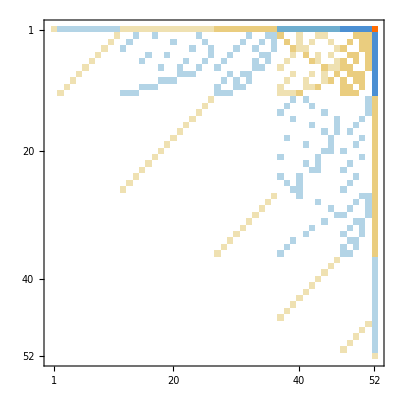
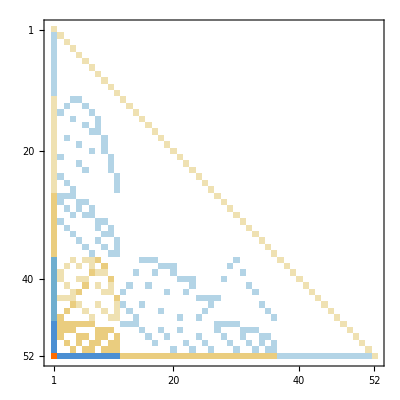
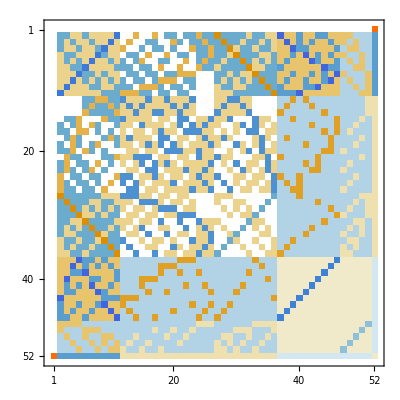
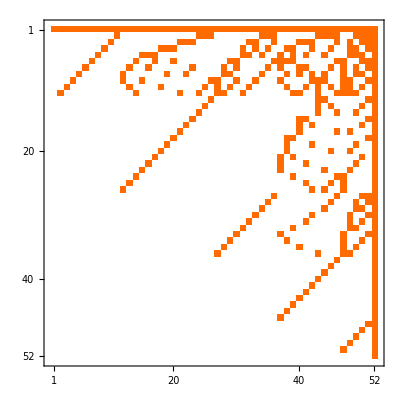
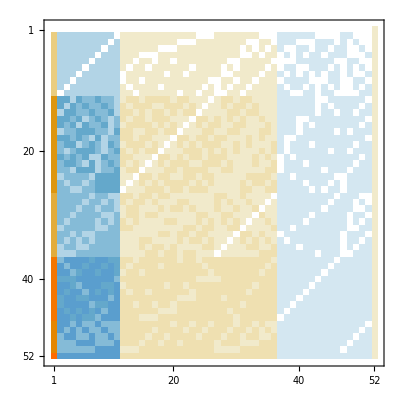
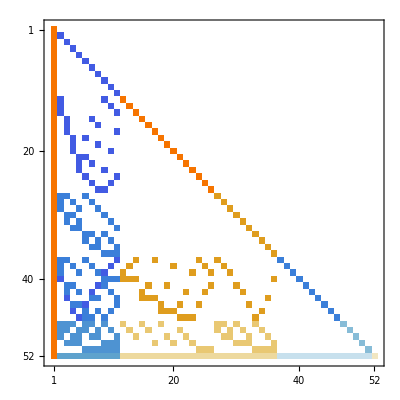
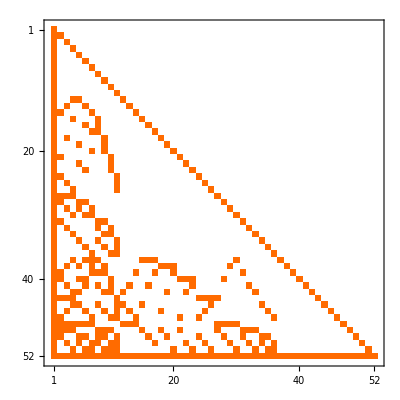
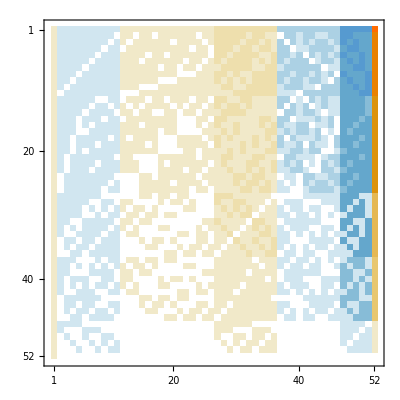
| C | E | G | F
C | -Graphics-C→C | -Graphics-C→E | -Graphics-C→G | -Graphics-C→F
E | -Graphics-E→C | -Graphics-E→E | -Graphics-E→G | -Graphics-E→F
G | -Graphics-G→C | -Graphics-G→E | -Graphics-G→G | -Graphics-G→F
F | -Graphics-F→C | -Graphics-F→E | -Graphics-F→G | -Graphics-F→F

```mathematica
With[{bases={"C","E","G","F"}},
TableForm[Table[Labeled[ConversionMatrix[base1,base2]//MatrixPlot,base1->base2],{base1,bases},{base2,bases}],TableHeadings->{bases, bases}]
]
```

```mathematica
(ConversionMatrix["C","G"].ConversionMatrix["F","E"]//Diagonal)
```

{1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-6,-6,-6,-6,-6,24}

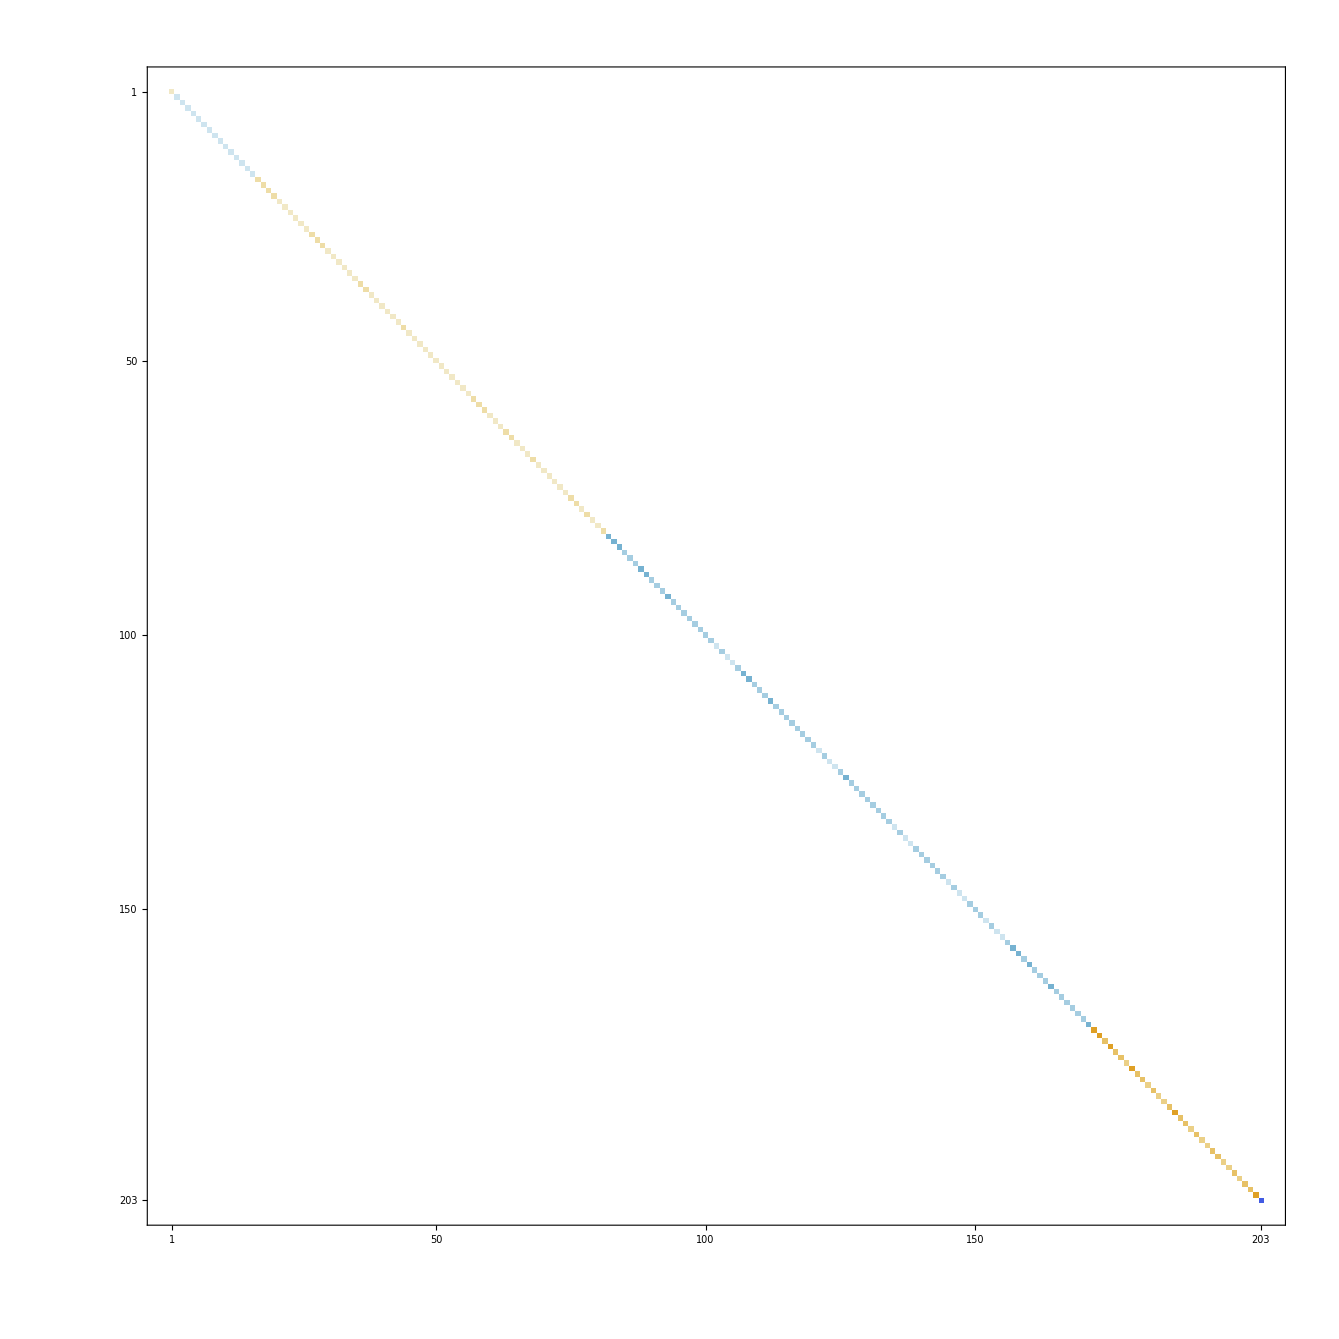

```mathematica
(ConversionMatrix6["C","G"].ConversionMatrix6["F","E"])//MatrixPlot
```

```mathematica
With[{bases={"C","E","G","F"}},
TableForm[Table[Labeled[ConversionMatrix[base1,base2]//MatrixPlot,base1->base2],{base1,bases},{base2,bases}],TableHeadings->{bases, bases}]
]
```

| C | E | G | F
C | -Graphics-C→C | -Graphics-C→E | -Graphics-C→G | -Graphics-C→F
E | -Graphics-E→C | -Graphics-E→E | -Graphics-E→G | -Graphics-E→F
G | -Graphics-G→C | -Graphics-G→E | -Graphics-G→G | -Graphics-G→F
F | -Graphics-F→C | -Graphics-F→E | -Graphics-F→G | -Graphics-F→F